```mathematica
Needs["PlotLegends`"]
```

```mathematica
ClearAll[NNVC,NNVV]
```

```mathematica
Do[

Do[

ll=ToString[l];
vv=ToString[v];

NNVC[v][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9DifferentLengths/v"<>vv<>"-l"<>ll<>"k-NNVCorr.txt",{Number,Number}];

NNVV[v][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9DifferentLengths/v"<>vv<>"-l"<>ll<>"k-NNVVariance.txt",{Number,Number}];

,{l,{5,10,20,30,50}}]

,{v,{4,5,6,7,8,9}}]
```

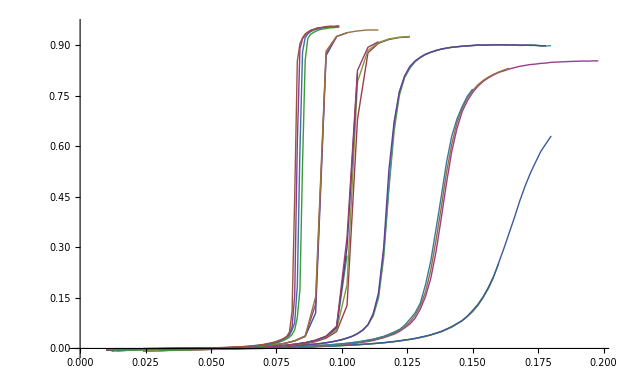

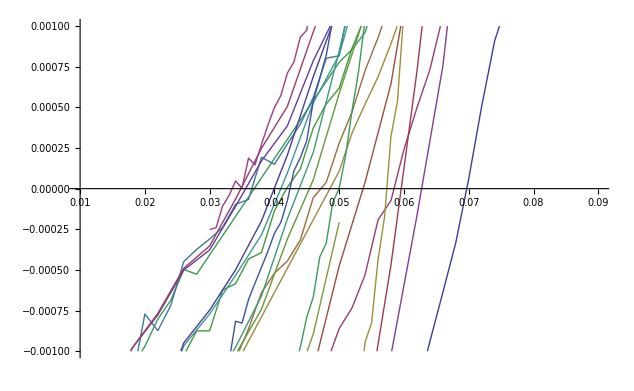

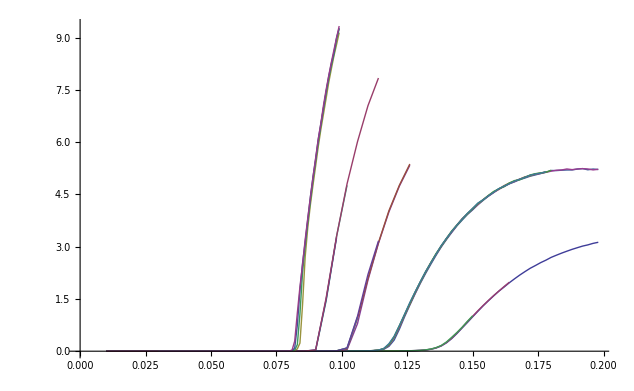

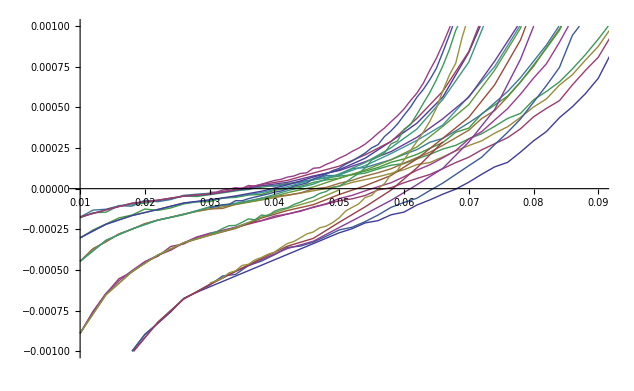

```mathematica
ListPlot[{NNVC[4][5],NNVC[4][10],NNVC[4][20],NNVC[4][30],NNVC[4][50],NNVC[5][5],NNVC[5][10],NNVC[5][20],NNVC[5][50],NNVC[6][5],NNVC[6][10],NNVC[6][20],NNVC[6][30],NNVC[6][50],NNVC[7][5],NNVC[7][10],NNVC[7][20],NNVC[7][30],NNVC[7][50],NNVC[8][5],NNVC[8][10],NNVC[8][20],NNVC[8][30],NNVC[8][50],NNVC[9][5],NNVC[9][10],NNVC[9][20],NNVC[9][50]},Joined->True]
ListPlot[{NNVC[5][5],NNVC[5][10],NNVC[5][20],NNVC[5][50],NNVC[6][5],NNVC[6][10],NNVC[6][20],NNVC[6][30],NNVC[6][50],NNVC[7][5],NNVC[7][10],NNVC[7][20],NNVC[7][30],NNVC[7][50],NNVC[8][5],NNVC[8][10],NNVC[8][20],NNVC[8][30],NNVC[8][50],NNVC[9][5],NNVC[9][10],NNVC[9][20],NNVC[9][50]},Joined->True,PlotRange->{{0.01,0.09},{-0.001,0.001}}]
ListPlot[{NNVV[5][5],NNVV[5][10],NNVV[5][20],NNVV[5][50],NNVV[6][5],NNVV[6][10],NNVV[6][20],NNVV[6][30],NNVV[6][50],NNVV[7][5],NNVV[7][10],NNVV[7][20],NNVV[7][30],NNVV[7][50],NNVV[8][5],NNVV[8][10],NNVV[8][20],NNVV[8][30],NNVV[8][50],NNVV[9][5],NNVV[9][10],NNVV[9][20],NNVV[9][50]},Joined->True]
ListPlot[{NNVV[5][5],NNVV[5][10],NNVV[5][20],NNVV[5][50],NNVV[6][5],NNVV[6][10],NNVV[6][20],NNVV[6][30],NNVV[6][50],NNVV[7][5],NNVV[7][10],NNVV[7][20],NNVV[7][30],NNVV[7][50],NNVV[8][5],NNVV[8][10],NNVV[8][20],NNVV[8][30],NNVV[8][50],NNVV[9][5],NNVV[9][10],NNVV[9][20],NNVV[9][50]},Joined->True,PlotRange->{{0.01,0.09},{-0.001,0.001}}]
```

```mathematica
Do[

Do[

ll=ToString[l];
vv=ToString[v];

VC[v][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9DifferentLengths/VCorr-v"<>vv<>"-l"<>ll<>"k.txt",{Number,Number,Number,Number,Number,Number}];

vc1[v][l]=VC[v][l][[All,1]];
vc2[v][l]=VC[v][l][[All,2]];
vc3[v][l]=VC[v][l][[All,3]];
vc4[v][l]=VC[v][l][[All,4]];
vc5[v][l]=VC[v][l][[All,5]];
vc6[v][l]=VC[v][l][[All,6]];

vbar[v][l]=Table[{vc1[v][l][[i]],vc2[v][l][[i]]},{i,1,Length[vc1[v][l]]}];
vbarn[v][l]=Table[{vc1[v][l][[i]],vc2[v][l][[i]]/v},{i,1,Length[vc1[v][l]]}];
vvar[v][l]=Table[{vc1[v][l][[i]],vc3[v][l][[i]]-vc2[v][l][[i]]*vc2[v][l][[i]]},{i,1,Length[vc1[v][l]]}];
vcn1[v][l]=Table[{vc1[v][l][[i]],(vc4[v][l][[i]]-vc2[v][l][[i]]*vc2[v][l][[i]])/(vc3[v][l][[i]]-vc2[v][l][[i]]*vc2[v][l][[i]])},{i,1,Length[vc1[v][l]]}];
vcn2[v][l]=Table[{vc1[v][l][[i]],(vc5[v][l][[i]]-vc2[v][l][[i]]*vc2[v][l][[i]])/(vc3[v][l][[i]]-vc2[v][l][[i]]*vc2[v][l][[i]])},{i,1,Length[vc1[v][l]]}];
vcn3[v][l]=Table[{vc1[v][l][[i]],(vc6[v][l][[i]]-vc2[v][l][[i]]*vc2[v][l][[i]])/(vc3[v][l][[i]]-vc2[v][l][[i]]*vc2[v][l][[i]])},{i,1,Length[vc1[v][l]]}];
vvn1[v][l]=Table[{vc1[v][l][[i]],(vc4[v][l][[i]]-vc2[v][l][[i]]*vc2[v][l][[i]])},{i,1,Length[vc1[v][l]]}];
vvn2[v][l]=Table[{vc1[v][l][[i]],(vc5[v][l][[i]]-vc2[v][l][[i]]*vc2[v][l][[i]])},{i,1,Length[vc1[v][l]]}];
vvn3[v][l]=Table[{vc1[v][l][[i]],(vc6[v][l][[i]]-vc2[v][l][[i]]*vc2[v][l][[i]])},{i,1,Length[vc1[v][l]]}];

,{l,{5,10,20,30,50}}]

,{v,{5,6,7,8,9}}]
```

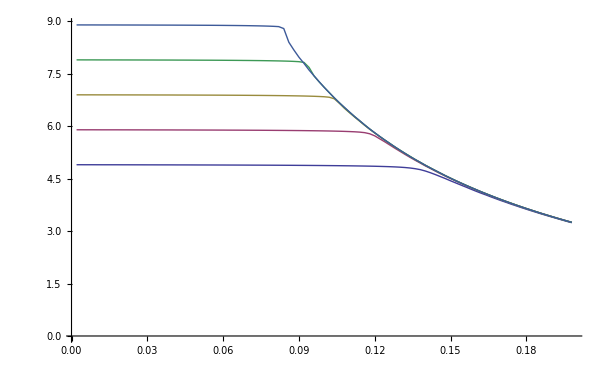

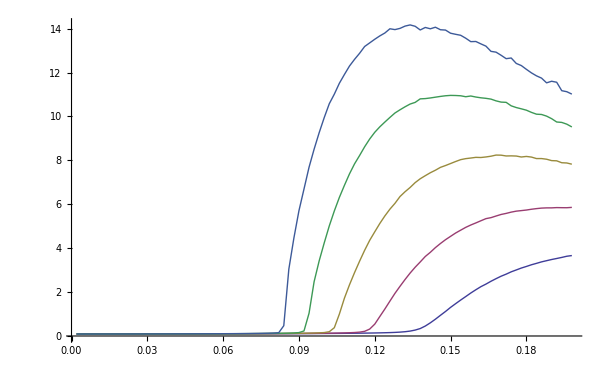

```mathematica
ListPlot[{vbar[5][5],vbar[6][5],vbar[7][5],vbar[8][5],vbar[9][5]},PlotRange->Full,Joined->True]
ListPlot[{vvar[5][5],vvar[6][5],vvar[7][5],vvar[8][5],vvar[9][5]},PlotRange->Full,Joined->True]
```

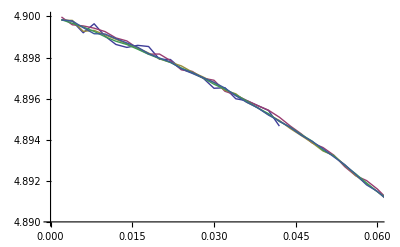

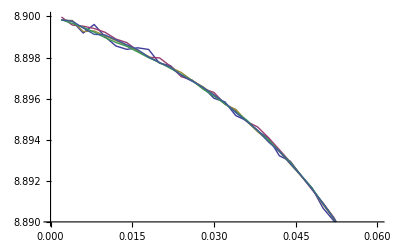

```mathematica
ListPlot[{vbar[5][5],vbar[5][10],vbar[5][20],vbar[5][30],vbar[5][50]},PlotRange->{{0,0.06},{4.89,4.9}},Joined->True]
ListPlot[{vbar[9][5],vbar[9][10],vbar[9][20],vbar[9][30],vbar[9][50]},PlotRange->{{0,0.06},{8.89,8.9}},Joined->True]
```

```mathematica
m=9;

d=0.05;
p=0.1;
α=p(1-p)/(1/d-m-0.5);

p*p*(m-2)+p*(1-p)*(m-1)+(1-p)*m
α*p*p*(m-3)+(α*p*(1-p)+(1-α)*p*p)*(m-2)+(α*(1-p)+(1-α)*p*(1-p))*(m-1)+(1-α)*(1-p)*m
```

8.89

8.88143

```mathematica
calcvav[m_,d_]:=p(1-p)/(1/d-m-0.5)*p*p*(m-3)+(p(1-p)/(1/d-m-0.5)*p*(1-p)+(1-p(1-p)/(1/d-m-0.5))*p*p)*(m-2)+(p(1-p)/(1/d-m-0.5)*(1-p)+(1-p(1-p)/(1/d-m-0.5))*p*(1-p))*(m-1)+(1-p(1-p)/(1/d-m-0.5))*(1-p)*m;
```

```mathematica
calcvav[9,0.1]
```

8.71

```mathematica
v=9;
l=10;
pic1=ListPlot[vbar[v][l],PlotRange->{Full,{8.6,8.9}},Joined->True];
pic2=Plot[calcvav[v,d],{d,0.0001,0.15},PlotRange->{Full,{0.9*v,v}},PlotStyle->{Red}];
```

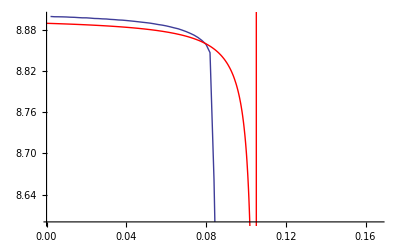

```mathematica
Show[{pic1,pic2}]
```

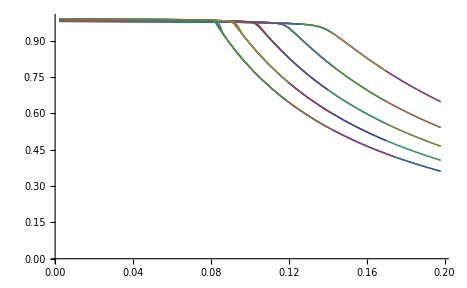

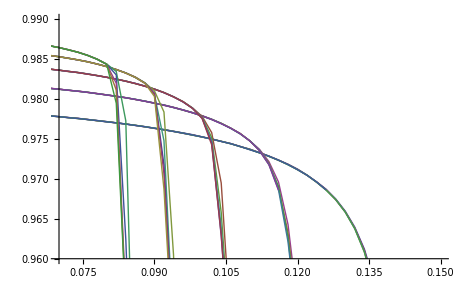

```mathematica
ListPlot[{vbarn[5][5],vbarn[5][10],vbarn[5][20],vbarn[5][30],vbarn[5][50],vbarn[6][5],vbarn[6][10],vbarn[6][20],vbarn[6][30],vbarn[6][50],vbarn[7][5],vbarn[7][10],vbarn[7][20],vbarn[7][30],vbarn[7][50],vbarn[8][5],vbarn[8][10],vbarn[8][20],vbarn[8][30],vbarn[8][50],vbarn[9][5],vbarn[9][10],vbarn[9][20],vbarn[9][30],vbarn[9][50]},PlotRange->Full,Joined->True]
ListPlot[{vbarn[5][5],vbarn[5][10],vbarn[5][20],vbarn[5][30],vbarn[5][50],vbarn[6][5],vbarn[6][10],vbarn[6][20],vbarn[6][30],vbarn[6][50],vbarn[7][5],vbarn[7][10],vbarn[7][20],vbarn[7][30],vbarn[7][50],vbarn[8][5],vbarn[8][10],vbarn[8][20],vbarn[8][30],vbarn[8][50],vbarn[9][5],vbarn[9][10],vbarn[9][20],vbarn[9][30],vbarn[9][50]},PlotRange->{{0.07,0.15},{0.96,0.99}},Joined->True]
```

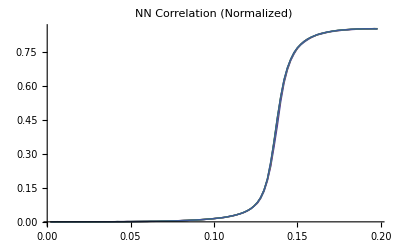

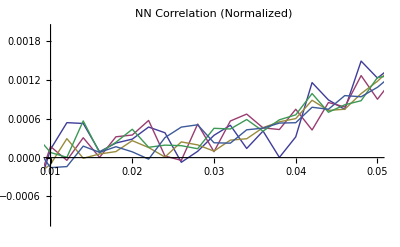

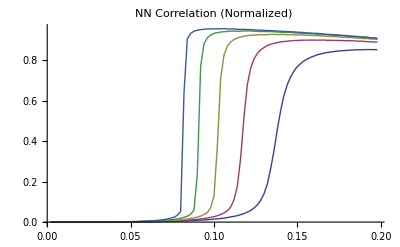

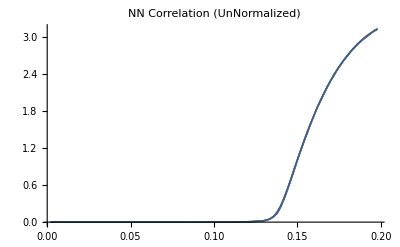

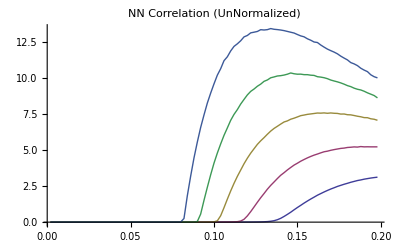

```mathematica
v=5;
l=50;
ListPlot[{vcn1[v][5],vcn1[v][10],vcn1[v][20],vcn1[v][30],vcn1[v][50]},PlotRange->Full,Joined->True,PlotLabel->"NN Correlation (Normalized)"]
ListPlot[{vcn1[v][5],vcn1[v][10],vcn1[v][20],vcn1[v][30],vcn1[v][50]},PlotRange->{{0.01,0.05},{-0.001,0.002}},Joined->True,PlotLabel->"NN Correlation (Normalized)"]
ListPlot[{vcn1[5][l],vcn1[6][l],vcn1[7][l],vcn1[8][l],vcn1[9][l]},PlotRange->Full,Joined->True,PlotLabel->"NN Correlation (Normalized)"]
ListPlot[{vvn1[v][5],vvn1[v][10],vvn1[v][20],vvn1[v][30],vvn1[v][50]},PlotRange->Full,Joined->True,PlotLabel->"NN Correlation (UnNormalized)"]
ListPlot[{vvn1[5][l],vvn1[6][l],vvn1[7][l],vvn1[8][l],vvn1[9][l]},PlotRange->Full,Joined->True,PlotLabel->"NN Correlation (UnNormalized)"]
```

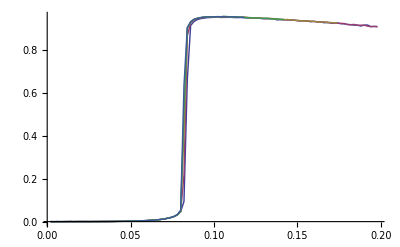

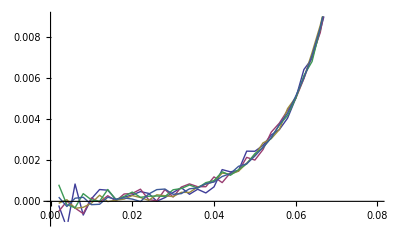

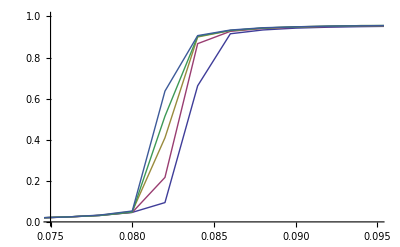

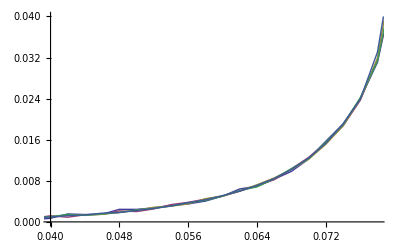

```mathematica
ListPlot[{vcn1[9][5],vcn1[9][10],vcn1[9][20],vcn1[9][30],vcn1[9][50]},PlotRange->Full,Joined->True]
ListPlot[{vcn1[9][5],vcn1[9][10],vcn1[9][20],vcn1[9][30],vcn1[9][50]},PlotRange->{{0,0.08},{-0.001,0.009}},Joined->True]
ListPlot[{vcn1[9][5],vcn1[9][10],vcn1[9][20],vcn1[9][30],vcn1[9][50]},PlotRange->{{0.075,0.095},{0,1}},Joined->True]
ListPlot[{vcn1[9][5],vcn1[9][10],vcn1[9][20],vcn1[9][30],vcn1[9][50]},PlotRange->{{0.04,0.078},{0,0.04}},Joined->True]
```

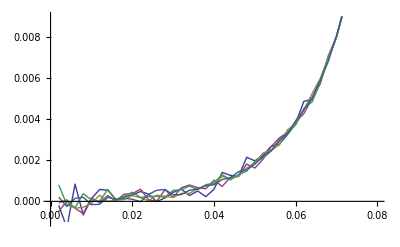

```mathematica
ListPlot[{vcn1[8][5],vcn1[8][10],vcn1[8][20],vcn1[8][30],vcn1[8][50]},PlotRange->{{0,0.08},{-0.001,0.009}},Joined->True]
```

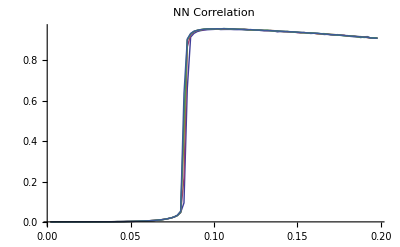

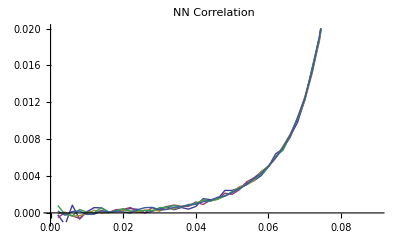

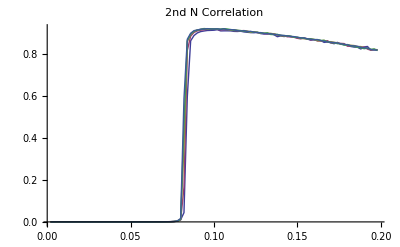

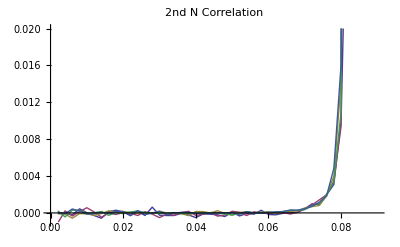

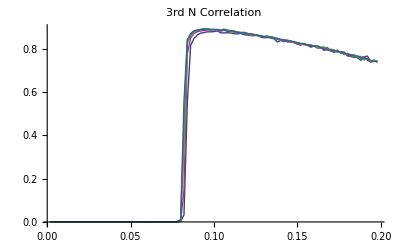

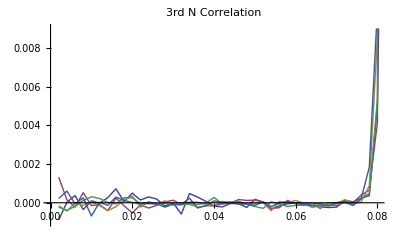

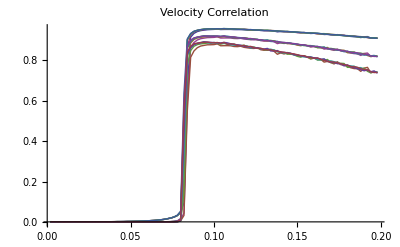

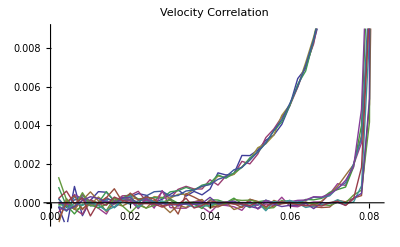

```mathematica
v=9;
ListPlot[{vcn1[v][5],vcn1[v][10],vcn1[v][20],vcn1[v][30],vcn1[v][50]},PlotRange->Full,Joined->True,PlotLabel->"NN Correlation"]
ListPlot[{vcn1[v][5],vcn1[v][10],vcn1[v][20],vcn1[v][30],vcn1[v][50]},PlotRange->{{0,0.09},{-0.001,0.02}},Joined->True,PlotLabel->"NN Correlation"]
ListPlot[{vcn2[v][5],vcn2[v][10],vcn2[v][20],vcn2[v][30],vcn2[v][50]},PlotRange->Full,Joined->True,PlotLabel->"2nd N Correlation"]
ListPlot[{vcn2[v][5],vcn2[v][10],vcn2[v][20],vcn2[v][30],vcn2[v][50]},PlotRange->{{0,0.09},{-0.001,0.02}},Joined->True,PlotLabel->"2nd N Correlation"]
ListPlot[{vcn3[v][5],vcn3[v][10],vcn3[v][20],vcn3[v][30],vcn3[v][50]},PlotRange->Full,Joined->True,PlotLabel->"3rd N Correlation"]
ListPlot[{vcn3[v][5],vcn3[v][10],vcn3[v][20],vcn3[v][30],vcn3[v][50]},PlotRange->{{0,0.08},{-0.001,0.009}},Joined->True,PlotLabel->"3rd N Correlation"]
ListPlot[{vcn1[v][5],vcn1[v][10],vcn1[v][20],vcn1[v][30],vcn1[v][50],vcn2[v][5],vcn2[v][10],vcn2[v][20],vcn2[v][30],vcn2[v][50],vcn3[v][5],vcn3[v][10],vcn3[v][20],vcn3[v][30],vcn3[v][50]},PlotRange->Full,Joined->True,PlotLabel->"Velocity Correlation"]
ListPlot[{vcn1[v][5],vcn1[v][10],vcn1[v][20],vcn1[v][30],vcn1[v][50],vcn2[v][5],vcn2[v][10],vcn2[v][20],vcn2[v][30],vcn2[v][50],vcn3[v][5],vcn3[v][10],vcn3[v][20],vcn3[v][30],vcn3[v][50]},Joined->True,PlotLabel->"Velocity Correlation",PlotRange->{{0,0.082},{-0.001,0.009}}]
ListLogPlot[{vcn1[v][5],vcn1[v][10],vcn1[v][20],vcn1[v][30],vcn1[v][50],vcn2[v][5],vcn2[v][10],vcn2[v][20],vcn2[v][30],vcn2[v][50],vcn3[v][5],vcn3[v][10],vcn3[v][20],vcn3[v][30],vcn3[v][50]},Joined->True,PlotLabel->"Velocity Correlation",PlotRange->{{0,0.082},{-0.001,0.009}}]
```

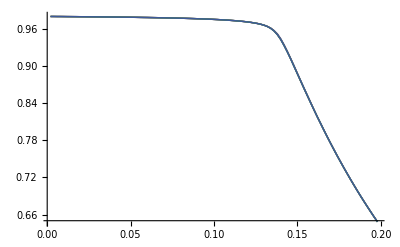

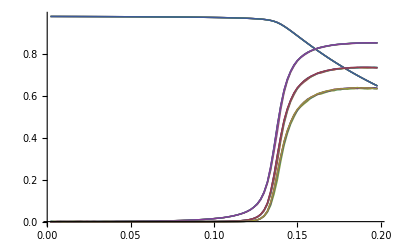

```mathematica
v=5;
ListPlot[{vbarn[v][5],vbarn[v][10],vbarn[v][20],vbarn[v][30],vbarn[v][50]},PlotRange->Full,Joined->True]
ListPlot[{vbarn[v][5],vbarn[v][10],vbarn[v][20],vbarn[v][30],vbarn[v][50],vcn1[v][5],vcn1[v][10],vcn1[v][20],vcn1[v][30],vcn1[v][50],vcn2[v][5],vcn2[v][10],vcn2[v][20],vcn2[v][30],vcn2[v][50],vcn3[v][5],vcn3[v][10],vcn3[v][20],vcn3[v][30],vcn3[v][50]},PlotRange->Full,Joined->True]
v=9;
ListPlot[{vbarn[v][5],vbarn[v][10],vbarn[v][20],vbarn[v][30],vbarn[v][50]},PlotRange->Full,Joined->True]
ListPlot[{vbarn[v][5],vbarn[v][10],vbarn[v][20],vbarn[v][30],vbarn[v][50],vcn1[v][5],vcn1[v][10],vcn1[v][20],vcn1[v][30],vcn1[v][50],vcn2[v][5],vcn2[v][10],vcn2[v][20],vcn2[v][30],vcn2[v][50],vcn3[v][5],vcn3[v][10],vcn3[v][20],vcn3[v][30],vcn3[v][50]},PlotRange->Full,Joined->True]
ListPlot[{vbarn[v][5],vbarn[v][10],vbarn[v][20],vbarn[v][30],vbarn[v][50]},PlotRange->Full,Joined->True]
ListLogPlot[{vbarn[v][5],vbarn[v][10],vbarn[v][20],vbarn[v][30],vbarn[v][50],vcn1[v][5],vcn1[v][10],vcn1[v][20],vcn1[v][30],vcn1[v][50],vcn2[v][5],vcn2[v][10],vcn2[v][20],vcn2[v][30],vcn2[v][50],vcn3[v][5],vcn3[v][10],vcn3[v][20],vcn3[v][30],vcn3[v][50]},PlotRange->Full,Joined->True]
```

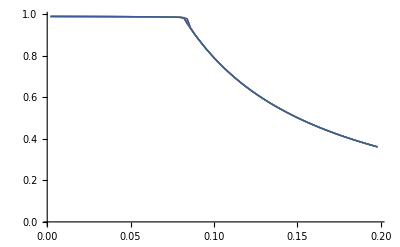
```mathematica
-Graphics-u
```

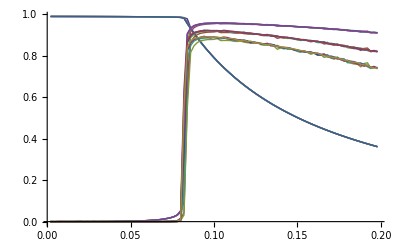

-Graphics-

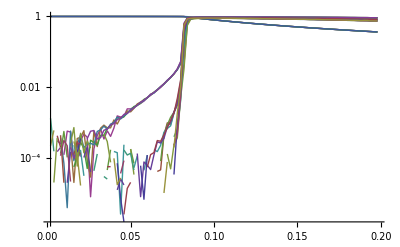

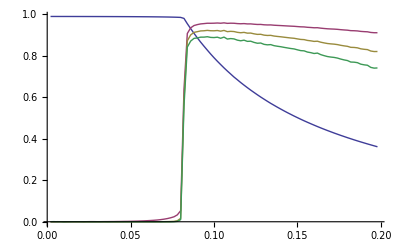

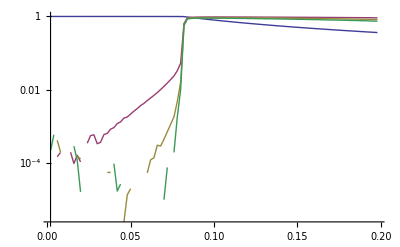

```mathematica
v=9;
l=50;
ListPlot[{vbarn[v][l],vcn1[v][l],vcn2[v][l],vcn3[v][l]},PlotRange->Full,Joined->True,PlotLegend->{"Normalized V bar","NN Correlation","2nd N Correlation","3rd N Correlation"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListLogPlot[{vbarn[v][l],vcn1[v][l],vcn2[v][l],vcn3[v][l]},PlotRange->Full,Joined->True,PlotLegend->{"Normalized V bar","NN Correlation","2nd N Correlation","3rd N Correlation"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```

```mathematica
Do[

Do[

ll=ToString[l];
vv=ToString[v];

VCf[v][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9DifferentLengths/VCorr-v"<>vv<>"-l"<>ll<>"k-fine.txt",{Number,Number,Number,Number,Number,Number}];

vc1f[v][l]=VCf[v][l][[All,1]];
vc2f[v][l]=VCf[v][l][[All,2]];
vc3f[v][l]=VCf[v][l][[All,3]];
vc4f[v][l]=VCf[v][l][[All,4]];
vc5f[v][l]=VCf[v][l][[All,5]];
vc6f[v][l]=VCf[v][l][[All,6]];

vbarf[v][l]=Table[{vc1f[v][l][[i]],vc2f[v][l][[i]]},{i,1,Length[vc1f[v][l]]}];
vbarnf[v][l]=Table[{vc1f[v][l][[i]],vc2f[v][l][[i]]/v},{i,1,Length[vc1f[v][l]]}];
vvarf[v][l]=Table[{vc1f[v][l][[i]],vc3f[v][l][[i]]-vc2f[v][l][[i]]*vc2f[v][l][[i]]},{i,1,Length[vc1f[v][l]]}];
vcn1f[v][l]=Table[{vc1f[v][l][[i]],(vc4f[v][l][[i]]-vc2f[v][l][[i]]*vc2f[v][l][[i]])/(vc3f[v][l][[i]]-vc2f[v][l][[i]]*vc2f[v][l][[i]])},{i,1,Length[vc1f[v][l]]}];
vcn2f[v][l]=Table[{vc1f[v][l][[i]],(vc5f[v][l][[i]]-vc2f[v][l][[i]]*vc2f[v][l][[i]])/(vc3f[v][l][[i]]-vc2f[v][l][[i]]*vc2f[v][l][[i]])},{i,1,Length[vc1f[v][l]]}];
vcn3f[v][l]=Table[{vc1f[v][l][[i]],(vc6f[v][l][[i]]-vc2f[v][l][[i]]*vc2f[v][l][[i]])/(vc3f[v][l][[i]]-vc2f[v][l][[i]]*vc2f[v][l][[i]])},{i,1,Length[vc1f[v][l]]}];

,{l,{5,10,20,30,50}}]

,{v,{9}}]
```

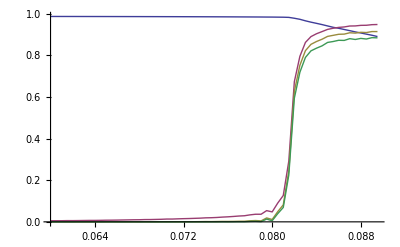

```mathematica
v=9;
l=50;
ListPlot[{vbarnf[v][l],vcn1f[v][l],vcn2f[v][l],vcn3f[v][l]},PlotRange->Full,Joined->True,PlotLegend->{"Normalized V bar","NN Correlation","2nd N Correlation","3rd N Correlation"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```

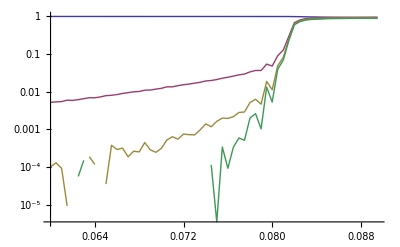

```mathematica
ListLogPlot[{vbarnf[v][l],vcn1f[v][l],vcn2f[v][l],vcn3f[v][l]},PlotRange->Full,Joined->True,PlotLegend->{"Normalized V bar","NN Correlation","2nd N Correlation","3rd N Correlation"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```